```mathematica
Binomial[7,3]
```

35

```mathematica
4^4
```

256

```mathematica
16
```

```mathematica
aaaa
aaab
aaac
aaad
aabb
aabc
aabd
aacc
aacd
aadd
abbb
abbc
abbd
abcc
abcd
abdd
accc
accd
acdd
addd
bbbb
bbbc
bbbd
bbcc
bbcd
bbdd
bccc
bccd
bcdd
bddd
cccc
cccd
ccdd
cddd
dddd
```

1

```mathematica
3/35//N
```

0.0857143

```mathematica
48/256
```

3/16

```mathematica
D[1/k Tan[(k π)/(2n + 1)],k]
```

(π Sec[(k π)/(1+2 n)]^2)/(k (1+2 n))-Tan[(k π)/(1+2 n)]/k^2

```mathematica
TrigReduce[(π Sec[(k π)/(1+2 n)]^2)/(k (1+2 n))-Tan[(k π)/(1+2 n)]/k^2]
```

(Sec[(k π)/(1+2 n)]^2 (2 k π-Sin[(2 k π)/(1+2 n)]-2 n Sin[(2 k π)/(1+2 n)]))/(2 k^2 (1+2 n))

```mathematica
f[k_]:=(π Sec[(k π)/(1+2 n)]^2)/(k (1+2 n))-Tan[(k π)/(1+2 n)]/k^2;
n=100;
```

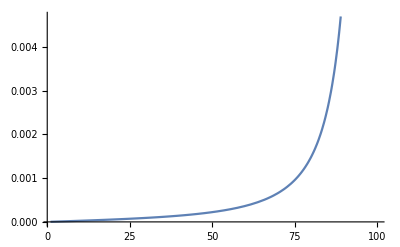

```mathematica
Plot[f[k],{k,1,n}]
```